```mathematica
(*This notebook computes the gravitational waveform and flux from a point particle falling at the speed of light into a BH. It is based on Refs.[1]-[3]. We use M=1 units here.*)
```

### Numerics in frequency - domain: Variation of constants

```mathematica
l=2;
la=1/2*(l-1)*(l+2);

ii=0;
Nmaxx=3000;
While[ii<Nmaxx+1,
w=0.00406+10^(-3)*ii;
r1=2*(1+10^(-4));
r2=200/w;
f=1-2/r;f1=D[f,r];
rt=Integrate[1/f,r];
EQ=f^2*D[y[r],{r,2}]+f*f1*D[y[r],{r,1}]+(w^2-f*(2*la^2*(la+1)*r^3+6*la^2*r^2+18*la*r+18)/(r^3*(la*r+3)^2))*y[r];

sol=NDSolve[{EQ==0,y[r1]==Exp[-I*w*(r1+2 Log[-2+r1])],y'[r1]==-I*w/(1-2/r1)*Exp[-I*w*(r1+2 Log[-2+r1])]},y,{r,r1,r2}(*,
            AccuracyGoal -> 12, PrecisionGoal -> 12,
                             WorkingPrecision -> 16,MaxSteps->340000*)];

ain=(ⅈ (-1-la))/w;bin=(-la^2-la^3+3 ⅈ (2 w+la w))/(2 la w^2);cin=(3 la^2 (4+la) w+ⅈ (-2 la^3-la^4+la^5-54 w^2-36 la w^2))/(6 la^2 w^3);din=(10 la^4+3 la^5-6 la^6+la^7-108 la^2 w^2-99 la^3 w^2+6 ⅈ w (7 la^3+2 la^5+108 w^2+72 la w^2))/(24 la^3 w^4);
aout=(ⅈ (1+la))/w;bout=(-la^2-la^3-3 ⅈ (2 w+la w))/(2 la w^2);cout=(3 la^2 (4+la) w+ⅈ (2 la^3+la^4-la^5+54 w^2+36 la w^2))/(6 la^2 w^3);
dout=(10 la^4+3 la^5-6 la^6+la^7-108 la^2 w^2-99 la^3 w^2-6 ⅈ w (7 la^3+2 la^5+108 w^2+72 la w^2))/(24 la^3 w^4);

yinf=y[r2]/.sol[[1]];yinf1=y'[r2]/.sol[[1]];
yinfana=Cin*(1+ain/r+bin/r^2+cin/r^3+din/r^4)*Exp[-I*w*rt]+Cout*(1+aout/r+bout/r^2+cout/r^3+dout/r^4)*Exp[I*w*rt]/.r->r2;
yinfana1=D[Cin*(1+ain/r+bin/r^2)*Exp[-I*w*rt]+Cout*(1+aout/r+bout/r^2)*Exp[I*w*rt],r]/.r->r2;
solcin=Solve[{yinf==yinfana,yinf1==yinfana1},{Cin,Cout}][[1]];

Aint=NIntegrate[-(8 I E^(-I w*(r+2 Log[-2+r])) √(2+4 l) (-2+l+l^2))/((6 +(-2+l+l^2) r)^2 w)*y[r]/.sol//Release,{r,r1,r2}(*,WorkingPrecision->8,PrecisionGoal->8,MaxRecursion->6*)][[1]];

answer[ii]={w,Psi=Aint/(2*I*w*Cin)/.solcin[[1]],P=1/(32*Pi)*(l-1)*l*(l+1)*(l+2)*w^2*Abs[Psi]^2};ii++]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.000959836739885546320720510760082788692670874297618865966796875}. NIntegrate obtained 0.000952974  - 0.00415223\ ⅈ
 and 4.29204×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.000959486249350558818328738031055991086759604513645172119140625}. NIntegrate obtained 0.000930531  - 0.00408674\ ⅈ
 and 4.28551×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.000959136074848985814740587318993902954389341175556182861328125}. NIntegrate obtained 0.000908555  - 0.00402229\ ⅈ
 and 4.28141×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

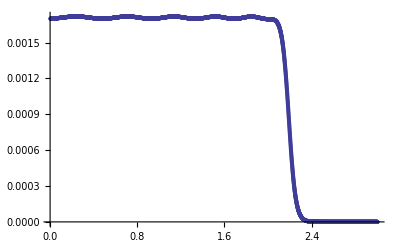

```mathematica
Tabe=Table[answer[ii],{ii,0,Nmaxx}];Tabeexport=Table[{N[Tabe[[i,1]]],Re[Tabe[[i,2]]],Im[Tabe[[i,2]]],Tabe[[i,3]]},{i,1,Length[Tabe]}];
Tabepower=Table[{Tabe[[i,1]],Tabe[[i,3]]},{i,1,Length[Tabe]}];ListPlot[Tabepower,PlotRange->All]
```

```mathematica
Export["C:\\Users\\Vitor\\Dropbox\\Mathematica_utils\\Infall\\Data\\InfallLight\Infall_light_HeadOn_l11.dat",Tabeexport]
```

C:\Users\Vitor\Dropbox\Mathematica_utils\Infall\Data\InfallLight\Infall_light_HeadOn_l11.dat

### Numerics in frequency - domain: Direct Integration

```mathematica
l=2;
la=1/2*(l-1)*(l+2);

INT[kkh_,w_]:=(


r1=2*(1+10^(-4));

r2=200/w;

f=1-2/r;f1=D[f,r];
rt=Integrate[1/f,r];
Source=-f*(8 I E^(-I w*(r+2 Log[-2+r])) √(2+4 l) (-2+l+l^2))/((6 +(-2+l+l^2) r)^2 w);
EQ=f^2*D[y[r],{r,2}]+f*f1*D[y[r],{r,1}]+(w^2-f*(2*la^2*(la+1)*r^3+6*la^2*r^2+18*la*r+18)/(r^3*(la*r+3)^2))*y[r];

sol=NDSolve[{EQ==Source,y[r1]==kkh*Exp[-I*w*(r1+2 Log[-2+r1])],y'[r1]==-kkh*I*w/(1-2/r1)*Exp[-I*w*(r1+2 Log[-2+r1])]},y,{r,r1,r2}(*,
            AccuracyGoal -> 12, PrecisionGoal -> 12,
                             WorkingPrecision -> 16,MaxSteps->340000*)];

ain=(ⅈ (-1-la))/w;bin=(-la^2-la^3+3 ⅈ (2 w+la w))/(2 la w^2);cin=(3 la^2 (4+la) w+ⅈ (-2 la^3-la^4+la^5-54 w^2-36 la w^2))/(6 la^2 w^3);din=(10 la^4+3 la^5-6 la^6+la^7-108 la^2 w^2-99 la^3 w^2+6 ⅈ w (7 la^3+2 la^5+108 w^2+72 la w^2))/(24 la^3 w^4);
aout=(ⅈ (1+la))/w;bout=(-la^2-la^3-3 ⅈ (2 w+la w))/(2 la w^2);cout=(3 la^2 (4+la) w+ⅈ (2 la^3+la^4-la^5+54 w^2+36 la w^2))/(6 la^2 w^3);
dout=(10 la^4+3 la^5-6 la^6+la^7-108 la^2 w^2-99 la^3 w^2-6 ⅈ w (7 la^3+2 la^5+108 w^2+72 la w^2))/(24 la^3 w^4);

yinf=y[r2]/.sol[[1]];yinf1=y'[r2]/.sol[[1]];
yinfana=Cin*(1+ain/r+bin/r^2+cin/r^3+din/r^4)*Exp[-I*w*rt]+Cout*(1+aout/r+bout/r^2+cout/r^3+dout/r^4)*Exp[I*w*rt]/.r->r2;
yinfana1=D[Cin*(1+ain/r+bin/r^2)*Exp[-I*w*rt]+Cout*(1+aout/r+bout/r^2)*Exp[I*w*rt],r]/.r->r2;
solcin=Solve[{yinf==yinfana,yinf1==yinfana1},{Cin,Cout}][[1]];


(*answer[ii]={w,Cin/.solcin,Cout/.solcin,P=1/(32*Pi)*(l-1)*l*(l+1)*(l+2)*w^2*Abs[Psi]^2};*)
Cin/.solcin)
```

```mathematica
Abs[INT[0.314517+5.99874I,0.1]]
```

0.00172304

```mathematica
kguess=0.3+6*I;
```

```mathematica
ii=0;
OMEGA=0.10+0.001*ii;
f4[Y_?NumberQ]:=INT[(*k*)Y,(*w*)OMEGA];
sol2=FindRoot[{f4[x1]==0},{x1,kguess}];
kguess=x1/.sol2
```

0.314517+5.99874 ⅈ

```mathematica
Table[
OMEGA=0.10+0.001*ii;
f4[Y_?NumberQ]:=INT[(*k*)Y,(*w*)OMEGA];
sol2=FindRoot[{f4[x1]==0},{x1,kguess}];
kguess=x1/.sol2;{OMEGA,1/(32*Pi)*(l-1)*l*(l+1)*(l+2)*OMEGA^2*Abs[yinf]^2},{ii,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{0.1,11.1404},{0.101,22.0844},{0.102,15.8411},{0.103,17.0608},{0.104,21.3146},{0.105,16.2042},{0.106,10.7016},{0.107,11.0607},{0.108,0.264058},{0.109,0.26404},{0.11,0.264021},{0.111,0.264003},{0.112,0.263984},{0.113,0.263965},{0.114,0.263947},{0.115,0.263928},{0.116,0.263908},{0.117,0.263889},{0.118,0.26387},{0.119,0.26385},{0.12,0.26383},{0.121,0.263811},{0.122,0.263791},{0.123,0.263771},{0.124,0.26375},{0.125,0.26373},{0.126,0.26371},{0.127,0.263689},{0.128,0.263668},{0.129,0.263647},{0.13,0.263626},{0.131,0.263605},{0.132,0.263584},{0.133,0.263562},{0.134,0.263541},{0.135,0.263519},{0.136,0.263497},{0.137,0.263475},{0.138,0.263453},{0.139,0.26343},{0.14,0.263408},{0.141,0.263385},{0.142,0.263362},{0.143,0.26334},{0.144,0.263316},{0.145,0.263293},{0.146,0.26327},{0.147,0.263246},{0.148,0.263222},{0.149,0.263198},{0.15,0.263174},{0.151,0.26315},{0.152,0.263126},{0.153,0.263101},{0.154,0.263076},{0.155,0.263051},{0.156,0.263026},{0.157,0.263001},{0.158,0.262975},{0.159,0.262949},{0.16,0.262923},{0.161,0.262897},{0.162,0.262871},{0.163,0.262844},{0.164,0.262817},{0.165,0.26279},{0.166,0.262763},{0.167,0.262735},{0.168,0.262708},{0.169,0.26268},{0.17,0.262651},{0.171,0.262623},{0.172,0.262594},{0.173,0.262565},{0.174,0.262536},{0.175,0.262506},{0.176,0.262477},{0.177,0.262446},{0.178,0.262416},{0.179,0.262385},{0.18,0.262354},{0.181,0.262323},{0.182,0.262291},{0.183,0.262259},{0.184,0.262227},{0.185,0.262194},{0.186,0.262161},{0.187,0.262127},{0.188,0.262093},{0.189,0.262059},{0.19,0.262024},{0.191,0.261989},{0.192,0.261953},{0.193,0.261917},{0.194,0.261881},{0.195,0.261843},{0.196,0.261806},{0.197,0.261768},{0.198,0.261729},{0.199,0.26169},{0.2,0.26165},{0.201,0.26161},{0.202,0.261569},{0.203,0.261527},{0.204,0.261485},{0.205,0.261442},{0.206,0.261399},{0.207,0.261354},{0.208,0.261309},{0.209,0.261263},{0.21,0.261217},{0.211,0.261169},{0.212,0.261121},{0.213,0.261072},{0.214,0.261022},{0.215,0.26097},{0.216,0.260918},{0.217,0.260865},{0.218,0.260811},{0.219,0.260756},{0.22,0.2607},{0.221,0.260642},{0.222,0.260583},{0.223,0.260523},{0.224,0.260462},{0.225,0.2604},{0.226,0.260336},{0.227,0.26027},{0.228,0.260203},{0.229,0.260135},{0.23,0.260065},{0.231,0.259993},{0.232,0.259919},{0.233,0.259844},{0.234,0.259767},{0.235,0.259688},{0.236,0.259607},{0.237,0.259524},{0.238,0.259439},{0.239,0.259351},{0.24,0.259261},{0.241,0.259169},{0.242,0.259075},{0.243,0.258978},{0.244,0.258878},{0.245,0.258775},{0.246,0.25867},{0.247,0.258562},{0.248,0.25845},{0.249,0.258336},{0.25,0.258218},{0.251,0.258097},{0.252,0.257972},{0.253,0.257844},{0.254,0.257712},{0.255,0.257576},{0.256,0.257436},{0.257,0.257292},{0.258,0.257143},{0.259,0.25699},{0.26,0.256833},{0.261,0.25667},{0.262,0.256503},{0.263,0.25633},{0.264,0.256152},{0.265,0.255969},{0.266,0.25578},{0.267,0.255585},{0.268,0.255384},{0.269,0.255176},{0.27,0.254962},{0.271,0.254741},{0.272,0.254514},{0.273,0.254279},{0.274,0.254036},{0.275,0.253786},{0.276,0.253528},{0.277,0.253261},{0.278,0.252986},{0.279,0.252703},{0.28,0.25241},{0.281,0.252108},{0.282,0.251796},{0.283,0.251474},{0.284,0.251142},{0.285,0.250799},{0.286,0.250445},{0.287,0.25008},{0.288,0.249703},{0.289,0.249314},{0.29,0.248913},{0.291,0.248499},{0.292,0.248071},{0.293,0.247631},{0.294,0.247176},{0.295,0.246707},{0.296,0.246223},{0.297,0.245724},{0.298,0.245209},{0.299,0.244678},{0.3,0.244131}}

```mathematica
Variation of Constants: 0.2642 at w=0.1, 0.261626820948879 at w=0.2 and 0.24405 at w=0.3
```

```mathematica
Export["C:\\Users\\Vitor\\Dropbox\\Mathematica_utils\\Infall\\Data\\InfallLight\Infall_light_HeadOn_l11.dat",Tabeexport]
```

C:\Users\Vitor\Dropbox\Mathematica_utils\Infall\Data\InfallLight\Infall_light_HeadOn_l11.dat

### Time - domain waveforms

```mathematica
SetDirectory["C:\\Users\\Vitor\\Dropbox\\Mathematica_utils\\Infall\\Data\\InfallLight"];FileNames[]
```

{Infall_light_Flux_l2.dat,Infall_light_Flux_l3.dat,Infall_light_Flux_l4.dat,Infall_light_Flux_l5.dat,Infall_light_Flux_l6.dat,Infall_light_Flux_l7.dat,Infall_light_Flux_l8.dat,Infall_light_HeadOn_l10.dat,Infall_light_HeadOn_l10_time_long.dat,Infall_light_HeadOn_l11.dat,Infall_light_HeadOn_l2.dat,Infall_light_HeadOn_l2_time.dat,Infall_light_HeadOn_l2_time_long.dat,Infall_light_HeadOn_l3.dat,Infall_light_HeadOn_l3_time.dat,Infall_light_HeadOn_l3_time_long.dat,Infall_light_HeadOn_l4.dat,Infall_light_HeadOn_l4_time.dat,Infall_light_HeadOn_l4_time_long.dat,Infall_light_HeadOn_l5.dat,Infall_light_HeadOn_l5_time.dat,Infall_light_HeadOn_l5_time_long.dat,Infall_light_HeadOn_l6.dat,Infall_light_HeadOn_l6_time.dat,Infall_light_HeadOn_l6_time_long.dat,Infall_light_HeadOn_l7.dat,Infall_light_HeadOn_l7_time.dat,Infall_light_HeadOn_l7_time_long.dat,Infall_light_HeadOn_l8.dat,Infall_light_HeadOn_l8_time.dat,Infall_light_HeadOn_l8_time_long.dat,Infall_light_HeadOn_l9.dat,Infall_light_HeadOn_l9_time_long.dat}

```mathematica
datx1=Import["Infall_light_HeadOn_l11.dat","Table"];dat1=Table[ {datx1[[i,1]],datx1[[i,2]]+I*datx1[[i,3]]},{i,1,Length[datx1]}];
```

```mathematica
b=Interpolation[dat1,InterpolationOrder->2];xfinal=b[[1]][[1]][[2]]
```

3.00406

```mathematica
i=0;j=0;While[i<800,(c=NIntegrate[Re[b[x]*Exp[-I*(i-400)/10*x]],{x,0.0001,xfinal}])&&(d[j]=c);(i=i+1)&&(j=j+1)];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000154032788071968066941942743230953283273265697062015533447265625}. NIntegrate obtained 0.00966073 and 4.51813×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000154032788071968066941942743230953283273265697062015533447265625}. NIntegrate obtained 0.00966176 and 4.23947×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000154032788071968066941942743230953283273265697062015533447265625}. NIntegrate obtained 0.00966278 and 3.84527×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

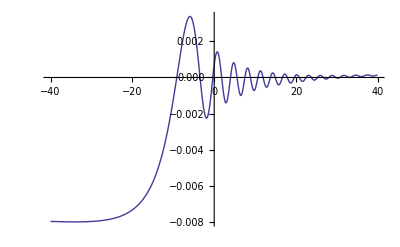

```mathematica
atime=Table[{N[(i-400)/10],-Sqrt[2/Pi]*d[i]-0.00025},{i,0,799}];

ListPlot[atime,PlotJoined -> True ,PlotRange->All]
```

```mathematica
Export["C:\\Users\\Vitor\\Dropbox\\Mathematica_utils\\Infall\\Data\\InfallLight\Infall_light_HeadOn_l11_time_long.dat",atime]
```

C:\Users\Vitor\Dropbox\Mathematica_utils\Infall\Data\InfallLight\Infall_light_HeadOn_l11_time_long.dat

### Fluxes

```mathematica
SetDirectory["C:\\Users\\Vitor Cardoso\\Dropbox\\Mathematica_utils\\Infall\\Data\\InfallLight"];FileNames[]
```

SetDirectory::cdir: Cannot set current directory to "C:\\Users\\Vitor Cardoso\\Dropbox\\Mathematica_utils\\Infall\\Data\\InfallLight".

{ANÚNCIO DE CONCURSO Agosto 2011.pdf,cruzadas_1.pdf,Default.rdp,desktop.ini,dybho_erc_logo.jpg,PP Congresso.pptx,WOW Slider}

```mathematica
SetDirectory["C:\\Users\\Vitor\\Dropbox\\Mathematica_utils\\Infall\\Data\\InfallLight"];FileNames[]
```

{Infall_light_Flux_l2.dat,Infall_light_Flux_l3.dat,Infall_light_Flux_l4.dat,Infall_light_Flux_l5.dat,Infall_light_Flux_l6.dat,Infall_light_Flux_l7.dat,Infall_light_Flux_l8.dat,Infall_light_HeadOn_l10.dat,Infall_light_HeadOn_l10_time_long.dat,Infall_light_HeadOn_l11.dat,Infall_light_HeadOn_l11_time_long.dat,Infall_light_HeadOn_l2.dat,Infall_light_HeadOn_l2_time.dat,Infall_light_HeadOn_l2_time_long.dat,Infall_light_HeadOn_l3.dat,Infall_light_HeadOn_l3_time.dat,Infall_light_HeadOn_l3_time_long.dat,Infall_light_HeadOn_l4.dat,Infall_light_HeadOn_l4_time.dat,Infall_light_HeadOn_l4_time_long.dat,Infall_light_HeadOn_l5.dat,Infall_light_HeadOn_l5_time.dat,Infall_light_HeadOn_l5_time_long.dat,Infall_light_HeadOn_l6.dat,Infall_light_HeadOn_l6_time.dat,Infall_light_HeadOn_l6_time_long.dat,Infall_light_HeadOn_l7.dat,Infall_light_HeadOn_l7_time.dat,Infall_light_HeadOn_l7_time_long.dat,Infall_light_HeadOn_l8.dat,Infall_light_HeadOn_l8_time.dat,Infall_light_HeadOn_l8_time_long.dat,Infall_light_HeadOn_l9.dat,Infall_light_HeadOn_l9_time_long.dat}

```mathematica
dat=Import["Infall_light_HeadOn_l2_time_long.dat","Table"];
l=2;datl2=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];

dat=Import["Infall_light_HeadOn_l3_time_long.dat","Table"];
l=3;datl3=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];

dat=Import["Infall_light_HeadOn_l4_time_long.dat","Table"];
l=4;datl4=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];

dat=Import["Infall_light_HeadOn_l5_time_long.dat","Table"];
l=5;datl5=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];

dat=Import["Infall_light_HeadOn_l6_time_long.dat","Table"];
l=6;datl6=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];

dat=Import["Infall_light_HeadOn_l7_time_long.dat","Table"];
l=7;datl7=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];

dat=Import["Infall_light_HeadOn_l8_time_long.dat","Table"];
l=8;datl8=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];

dat=Import["Infall_light_HeadOn_l9_time_long.dat","Table"];
l=9;datl9=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];

dat=Import["Infall_light_HeadOn_l10_time_long.dat","Table"];
l=10;datl10=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];

dat=Import["Infall_light_HeadOn_l11_time_long.dat","Table"];
l=11;datl11=Table[ {dat[[i,1]],Sqrt[(l+2)!/(64*Pi*(l-2)!)]*dat[[i,2]]},{i,1,Length[dat]}];
```

```mathematica
X11=Interpolation[datl11,InterpolationOrder->2];
X10=Interpolation[datl10,InterpolationOrder->2];
X9=Interpolation[datl9,InterpolationOrder->2];
X8=Interpolation[datl8,InterpolationOrder->2];
X7=Interpolation[datl7,InterpolationOrder->2];
X6=Interpolation[datl6,InterpolationOrder->2];
X5=Interpolation[datl5,InterpolationOrder->2];
X4=Interpolation[datl4,InterpolationOrder->2];
X3=Interpolation[datl3,InterpolationOrder->2];
X2=Interpolation[datl2,InterpolationOrder->2];
```

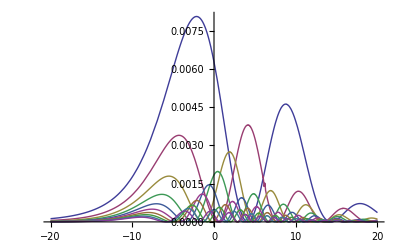

```mathematica
Plot[{X2'[t]^2,X3'[t]^2,X4'[t]^2,X5'[t]^2,X6'[t]^2,X7'[t]^2,X8'[t]^2,X9'[t]^2,X10'[t]^2,X11'[t]^2},{t,-20,20},PlotRange->All]
```

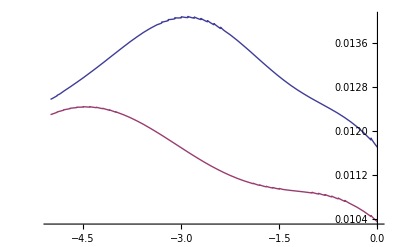

```mathematica
Plot[{X2'[t]^2+X3'[t]^2+X4'[t]^2+X5'[t]^2+X6'[t]^2+X7'[t]^2+X8'[t]^2+X9'[t]^2+X10'[t]^2+X11'[t]^2,X2'[t]^2+X3'[t]^2+X4'[t]^2+X5'[t]^2+X6'[t]^2},{t,-5,0},PlotRange->All]
```

```mathematica
Sum[1/xx,{xx,2,11}]/Sum[1/xx,{xx,2,6}]//N
```

1.39302

```mathematica
-Integrate[1/(1-2/r),r]/.r->2.2//N
```

1.01888

```mathematica
{X2'[-3]^2,X3'[-3]^2,X4'[-3]^2,X5'[-3]^2,X6'[-3]^2,X7'[-3]^2,X8'[-3]^2,X9'[-3]^2,X10'[-3]^2,X11'[-3]^2}
```

{1.57051,0.600634,0.155265,0.00967861,0.0140388,0.0682739,0.113174,0.12461,0.10424,0.0674712}

```mathematica
10/9*0.104
```

0.115556

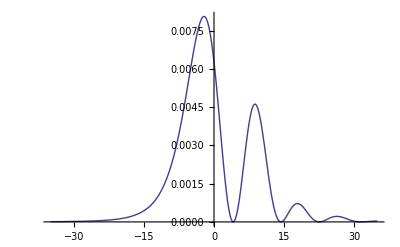

```mathematica
Fluxtime=Table[{N[t/20],X2'[t/20]^2},{t,-700,700}];
ListPlot[Fluxtime,PlotJoined->True,PlotRange->All]
```

```mathematica
<<NumericalMath`ListIntegrate`
```

General::newpkg: "NumericalMath`ListIntegrate`" is now available as the "Function Approximations Package". See the Compatibility Guide for updating information.

```mathematica
ListIntegrate[Fluxtime,2]
```

0.0985923

```mathematica
Export["C:\\Users\\Vitor Cardoso\\Dropbox\\Mathematica_utils\\Infall\\Data\\InfallLight\Infall_light_Flux_l8.dat",Fluxtime]
```

C:\Users\Vitor Cardoso\Dropbox\Mathematica_utils\Infall\Data\InfallLight\Infall_light_Flux_l8.dat

```mathematica
funcao=Sum[En[[l]]*1/((l-1)*(l)*(l+1)*(l+2))*(2*D[SphericalHarmonicY[l,0,theta,0],{theta,2}]+l*(l+1)*SphericalHarmonicY[l,0,theta,0])^2,{l,2,40}];
```

```mathematica
N[funcao]
```

### Expansion at infinity

```mathematica
f=1-2/r;f1=D[f,r];rt=Integrate[1/f,r];
y=Cin*(1+ain/r+bin/r^2+cin/r^3+din/r^4)*Exp[-I*w*rt]+Cout*(1+aout/r+bout/r^2+cout/r^3+dout/r^4)*Exp[I*w*rt]*0;
```

```mathematica
ain=(ⅈ (-1-la))/w;bin=(-la^2-la^3+3 ⅈ (2 w+la w))/(2 la w^2);cin=(3 la^2 (4+la) w+ⅈ (-2 la^3-la^4+la^5-54 w^2-36 la w^2))/(6 la^2 w^3);din=(10 la^4+3 la^5-6 la^6+la^7-108 la^2 w^2-99 la^3 w^2+6 ⅈ w (7 la^3+2 la^5+108 w^2+72 la w^2))/(24 la^3 w^4);
aout=(ⅈ (1+la))/w;bout=(-la^2-la^3-3 ⅈ (2 w+la w))/(2 la w^2);cout=(3 la^2 (4+la) w+ⅈ (2 la^3+la^4-la^5+54 w^2+36 la w^2))/(6 la^2 w^3);
dout=(10 la^4+3 la^5-6 la^6+la^7-108 la^2 w^2-99 la^3 w^2-6 ⅈ w (7 la^3+2 la^5+108 w^2+72 la w^2))/(24 la^3 w^4);
```

```mathematica
EQ=f^2*D[y,{r,2}]+f*f1*D[y,{r,1}]+(w^2-f*(2*la^2*(la+1)*r^3+6*la^2*r^2+18*la*r+18)/(r^3*(la*r+3)^2))*y;
expanded=Normal[Simplify[Series[Exp[I*w*rt]*EQ,{r,Infinity,5}]]]
```

-(ⅈ Cin (10 la^4-6 la^6+la^7+3 la^5 (1+4 ⅈ w)-108 la^2 w^2+648 ⅈ w^3+432 ⅈ la w^3-3 la^3 w (-14 ⅈ+33 w+8 din w^3)))/(3 la^3 r^5 w^3)

```mathematica
Simplify[Solve[expanded==0,din][[1]]]
```

{din→(10 la^4+3 la^5-6 la^6+la^7-108 la^2 w^2-99 la^3 w^2+6 ⅈ w (7 la^3+2 la^5+108 w^2+72 la w^2))/(24 la^3 w^4)}

## References

```mathematica
[1] V. Cardoso and J. P. S. Lemos, "Gravitational radiation from collisions at the speed of light: A Massless particle falling into a Schwarzschild black hole". PPhys.Lett.B538 (2002) 1-5.
```

```mathematica
[2]E. Berti, V. Cardoso and C. M. Will, "On gravitational-wave spectroscopy of massive black holes with the space interferometer LISA", Phys. Rev. D73:064030 (2006). [arXiv: gr-qc/0512160].
```

```mathematica
[3]E. Berti, V. Cardoso, T. Hinderer, M. Lemos, F. Pretorius, U. Sperhake and N. Yunes, "Semianalytical estimates of scattering thresholds and gravitational radiation in ultrarelativistic black hole encounters", Phys.Rev.D81 (2010) 104048.

[4]V. Cardoso, L. Gualtieri, C. Herdeiro, U. Sperhake, "Exploring New Physics Frontiers Through Numerical Relativity", Living Rev.Relativity 18 (2015) 1 
[5](The classical original work)M. Davis, R. Ruffini, W. H. Press and R. Price, "Gravitational radiation from a particle falling radially into a schwarzschild black hole", Phys.Rev.Lett.27 (1971) 1466-1469
```

```mathematica
[6]https://centra.tecnico.ulisboa.pt/network/grit/files/
```